```mathematica
Quit[];
```

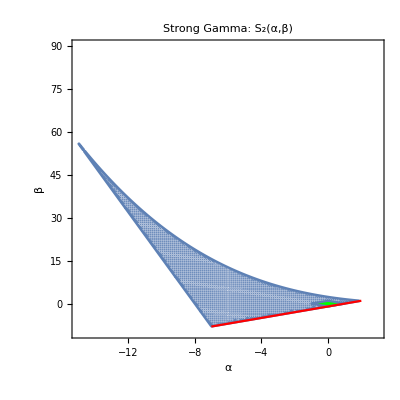

```mathematica
(*smallest stability region for Strong Gamma*)
p2=Show[RegionPlot[-8(x+8)<y&&y>x-1&&y<(8-x)^3/216,{x,-15,3},{y,-10,90},PlotPoints->150],RegionPlot[Abs[x]+Abs[y]<1,{x,-1,1},{y,-1,1},PlotStyle->Green],Plot[x-1,{x,-7,2},PlotStyle->Red],PlotLabel->"Strong Gamma: S_2(α,β)",LabelStyle->Directive[Bold,Black, FontSize->12],FrameLabel->{"α","β"},ImageSize->{Automatic, 300}]
```

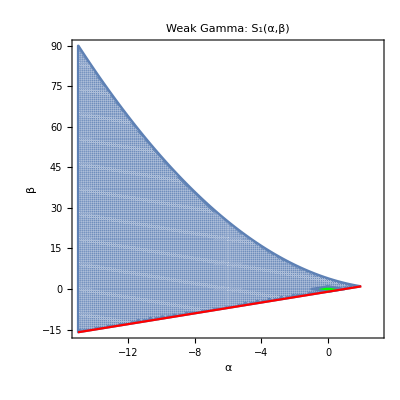

```mathematica
(*smallest stability region for Weak Gamma*)
p1=Show[RegionPlot[x-1<y<(2-x/2)^2,{x,-15,3},{y,-16,90},PlotPoints->150],RegionPlot[Abs[x]+Abs[y]<1,{x,-1,1},{y,-1,1},PlotStyle->Green],Plot[x-1,{x,-15,2},PlotStyle->Red],PlotLabel->"Weak Gamma: S_1(α,β)",LabelStyle->Directive[Bold,Black, FontSize->12],FrameLabel->{"α","β"},ImageSize->{Automatic, 300}]
```

```mathematica
(*Dirac kernel*)
H[z_]:=Exp[-z];
Q[t_,z_]:=(z+t)/(t*H[z]);
al[t_,w_]:=2*Re[Q[t,I*w]];
be[t_,w_]:=Abs[Q[t,I*w]]^2;
Co[t_,w_]:=Re[H[I*w]];
w1[t_]:=w/.FindRoot[Im[Q[t,I*w]]==0,{w,Pi/2,Pi}];
```

```mathematica
(*stability region for Dirac*)
pd[t_]:=Show[RegionPlot[y>1/Co[t,w1[t]]*(x-1/Co[t,w1[t]])&&y>x-1&&x<2(Cos[t*Sqrt[y-1]]-Sqrt[y-1]*Sin[t*Sqrt[y-1]]),{x,-15,3},{y,-5,15},PlotPoints->150],
RegionPlot[Abs[x]-1<y<1,{x,-2,2},{y,-1,1}],
RegionPlot[Abs[x]+Abs[y]<1,{x,-1,1},{y,-1,1},PlotStyle->Green],Plot[x-1,{x,-2.8,2},PlotStyle->Red],PlotLabel->"Dirac: S_0.5(α,β) and S_∞(α,β)",LabelStyle->Directive[Bold,Black, FontSize->12],FrameLabel->{"α","β"},ImageSize->{Automatic, 300},PlotRange->{{-15, 3},{-10,80}}]
```

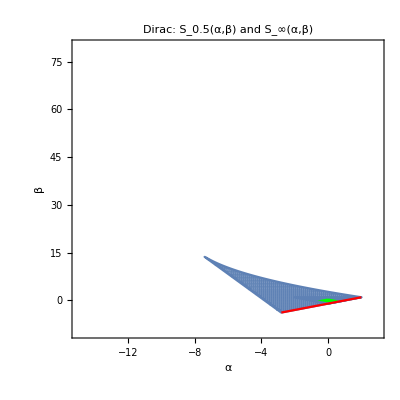

```mathematica
p3=pd[0.5]
```

```mathematica
p5=Grid[{{p3,p1,p2}}]
```